## Introduction

Code used in paper “Collective behaviour of swarmalators on a 1D ring”

## Main

### Dynamic simulation

```mathematica
(*Preamble*)
{dt,n,T}={0.25,100,100}; 
(*{J,k}={1,1}; *)  (*Static sync / π state, depending on IC*)
{J,k}={1,-0.5}; (*Static phase wave*)
(*{J,k}={1,-1.05};*) (*Active async*)
(*{J,k}={1,-3};*) (*Static async*)

{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
results=plotResults[znew]
]
```

### Static simulation

#### Simulation

```mathematica
(*Preample*)
{dt,n,T}={0.5,100,100}; 
{J,k}={1,-0.5};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
{Wps,Wms}={{},{}};
ts={};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Wp,Wm}=findWs[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
]
```

#### Plots

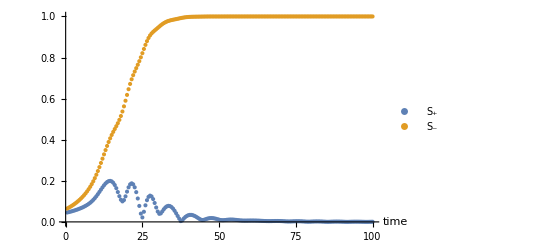

```mathematica
ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"S_+","S_-"}]
```

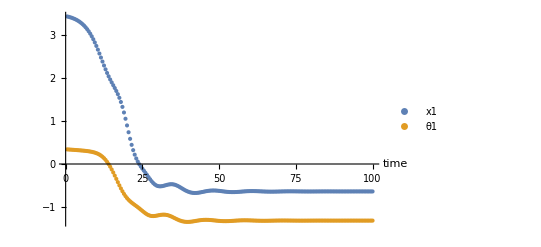

```mathematica
swarmalatorIndex=1;
ListPlot[{{ts,xs[[All,swarmalatorIndex]]}ᵀ,{ts,θs[[All,swarmalatorIndex]]}ᵀ},AxesLabel->{Style["time",13]},
PlotLegends->{"x"<>ToString[swarmalatorIndex],"θ"<>ToString[swarmalatorIndex]}]
```

```mathematica
Manipulate[ListPlot[{xs[[t,All]]//mod,θs[[t,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}],{t,1,Dimensions[xs][[2]],1}]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji] Cos[thetaji];
thetatemp=k*Sin[thetaji] Cos[xji];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_]:=Block[{colors,Wp,Wm,p1,p2,p3,x,θ},
{x,θ}={z[[1,All]],z[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

Return[Grid[{{p1,p2,p3}}]
]
];


eulerStep[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k];
k2=F[z+dt/2 k1,n,J,k];
k3=F[z+dt/2 k2,n,J,k];
k4=F[z+dt k3,n,J,k];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];
```